1. NARAVNA ŠTEVILA
 V prvih treh mesecih letošnjega leta so prodali veliko novih avtomobilov. V tabeli je število
prodanih avtomobilov treh avtomobilskih znamk v vsakem mesecu. Izpolni tabelo, nato pa
odgovori na vprašanja:
a) Katerih avtomobilov so v prvem trimesečju prodali največ?
b) V katerem mesecu so prodali največ avtomobilov?
c) V katerem mesecu so prodali najmanj Toyot?

```mathematica
Grid[{{Item["",Background->Lighter[Gray,.8],Frame->True],"januar","februar","marec",Item["Skupaj",Background->Lighter[Gray,.8],Frame->True]},{"Opel",401,199,255,401+199+255},{"Renault",318,507,387,318+507+387},{"Toyota",205,293,328,205+293+328},{Item["Skupaj",Background->Lighter[Gray,.8],Frame->True],401+318+205,199+507+293,255+387+328,855+1212+826}},Frame->All,ItemStyle->14,Spacings->{Automatic,.8},Alignment->{{Left,{Center}}},ItemSize->{{8,6,5,5}}]
```

| januar | februar | marec | Skupaj
Opel | 401 | 199 | 255 | 855
Renault | 318 | 507 | 387 | 1212
Toyota | 205 | 293 | 328 | 826
Skupaj | 924 | 999 | 970 | 2893

```mathematica
a= Max[855,1212,826]
```

1212

```mathematica
b=Max[924,999,970]
```

999

```mathematica
c=Min[205,293,328]
```

205

a) V prvem trimesečju so prodali največ avtomobilov Renault.
b) Največ avtomobilov so prodali v mesecu februarju.
c) Najmanj Toyot so prodali v mesecu januarju.

2. POTENCE
Poenostavi:

```mathematica
Simplify[(x^-2 y^3)^4/(x^-5 y^-4)^-2]
```

0.135114/x^18

```mathematica
Simplify[((x^3 y^4)/(x^-5 y))^-2]
```

1/(x^16 y^6)

```mathematica
Simplify[(x^-7 y^2)^-3/(x^8 y^-4)^5]
```

y^14/x^19

```mathematica
Simplify[(x^2 y^-4)^-3/(x^-4 y^5)^-2]
```

y^22/x^14

```mathematica
Simplify[(x^-2 y)^3*(x^4 y^9)^-2/(x^2 y^3)^-7]
```

y^6

```mathematica
Simplify[(x^-2 y^3)^-4*(x^-3 y^-1)^-8/(x^-16 y^-7)^-2]
```

1/y^18

3.RAČUNANJE Z IZRAZI
 Izpostavi in razstavi:

```mathematica
FullSimplify[2 z^2+14z+24]
```

2 (3+z) (4+z)

```mathematica
FullSimplify[3 z^2-9z-30]
```

3 (-5+z) (2+z)

```mathematica
FullSimplify[-2 z^2-22z-60]
```

-2 (5+z) (6+z)

```mathematica
FullSimplify[4 z^2+16z-84]
```

4 (-3+z) (7+z)

4. RAČUNANJE S KORENI
Kvadriraj:

```mathematica
Simplify[(2 √5-√2)^2]
```

22-4 √10

```mathematica
Simplify[(4 √6+√3)^2]
```

99+24 √2

```mathematica
Simplify[(3 √8-2 √5)^2]
```

92-24 √10

```mathematica
Simplify[(5 √2+2 √6)^2]
```

74+40 √3

```mathematica
Simplify[(3 √3-2 √8)^2]
```

59-24 √6

```mathematica
Simplify[(7 √8-5 √2)^2]
```

162

5. SISTEM LINEARNIH ENAČB
Grafično reši sistem linearnih enačb:

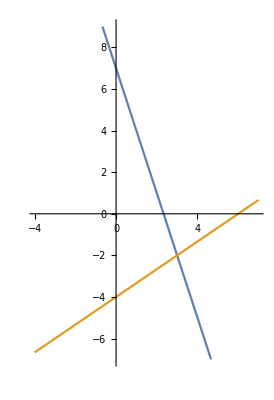

```mathematica
Plot[{y=-3x+7,y=2/3 x-4},{x,7,-4},PlotRange->{-7,9},AspectRatio->Automatic]
```

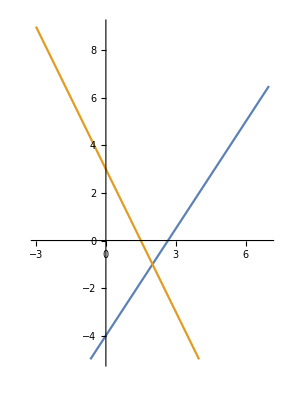

```mathematica
Plot[{y=3/2 x-4,y=-2x+3},{x,7,-4},PlotRange->{9,-5},AspectRatio->Automatic]
```

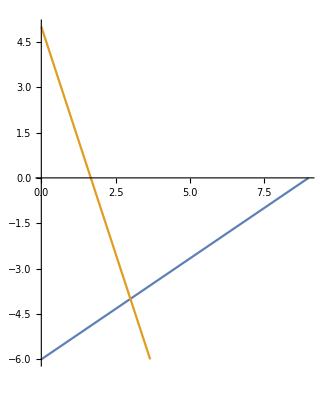

```mathematica
Plot[{y=2/3 x-6,y=-3x+5},{x,9,-7},PlotRange->{5,-6},AspectRatio->Automatic]
```

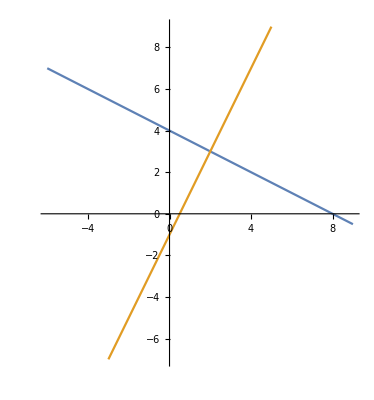

```mathematica
Plot[{y=-1/2 x+4,y=2x-1},{x,9,-6},PlotRange->{-7,9},AspectRatio->Automatic]
```

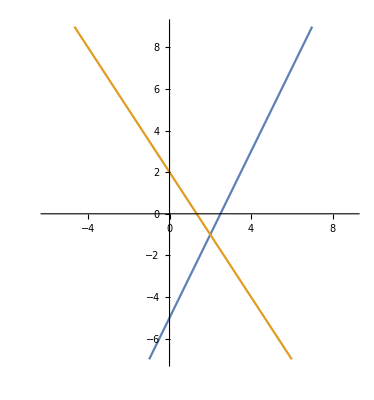

```mathematica
Plot[{y=-5+2x,y=(4-3x)/2},{x,9,-6},PlotRange->{-7,9},AspectRatio->Automatic]
```

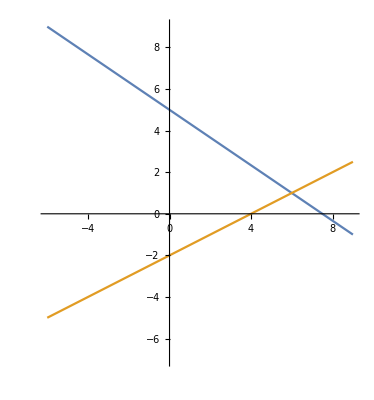

```mathematica
Plot[{y=(15-2x)/3,y=(-4+x)/2},{x,9,-6},PlotRange->{-7,9},AspectRatio->Automatic]
```

6. KVADRATNA ENAČBA
Okrajšaj ulomek:

```mathematica
FullSimplify[(x^2-2x-15)/(3 x^2-14x-5)]
```

(3+x)/(1+3 x)

```mathematica
FullSimplify[(2 x^2+9x-5)/(x^2+7x+10)]
```

2-5/(2+x)

```mathematica
FullSimplify[(2 x^2-18)/(5 x^2+13x-6)]
```

(2 (-3+x))/(-2+5 x)

```mathematica
FullSimplify[(4 x^2-19x+12)/(12 x^2-x-6)]
```

(-4+x)/(2+3 x)

7. SORAZMERJA IN ODSTOTKI
Osemnajst instalaterjev bi moralo montirati radiatorje v novi šoli tako, da bi vsak poskrbel za
osemindvajset radiatorjev. Žal so štirje delavci zboleli, zato morajo ostali narediti več. Koliko
radiatorjev bo moral montirati vsak od zdravih delavcev?

8. POLINOMI -1 
Deli in rezultat zapiši v obliki p(x)=k(x)*q(x)+o(x):

```mathematica
PolynomialRemainder[(3 x^5+3 x^4+14 x^3+10x+2),(3 x^2+2x-1),x]
```

-29/27+(565 x)/27

9. RACIONALNA FUNKCIJA
Nariši graf racionalne funkcije:

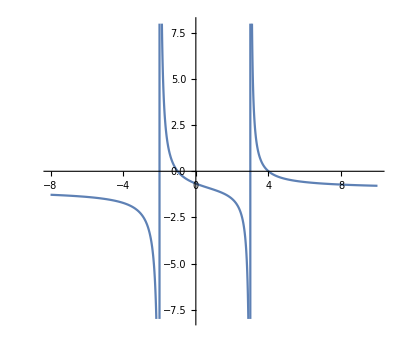

```mathematica
graf1 =Plot[{y=(-x^2+3x+4)/(x^2-x-6)},{x,-8,10},AspectRatio->Automatic,PlotRange->{-8,8}]
```

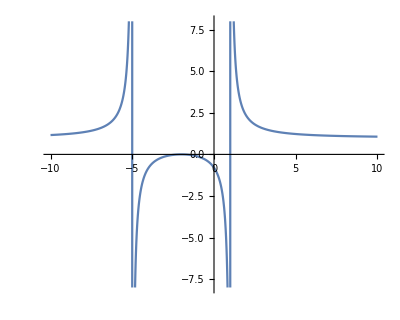

```mathematica
Plot[{y=(x^2+4x+4)/(x^2+4x-5)},{x,-10,10},AspectRatio->Automatic,PlotRange->{-8,8}]
```

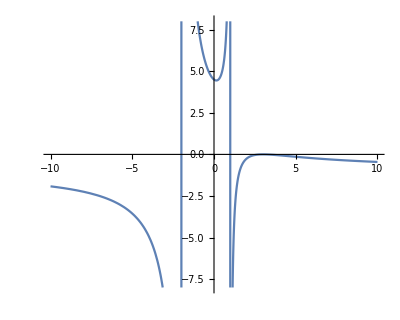

```mathematica
Plot[{y=(x^2-6x+9)/(-x^2-x+2)},{x,-10,10},AspectRatio->Automatic,PlotRange->{-8,8}]
```

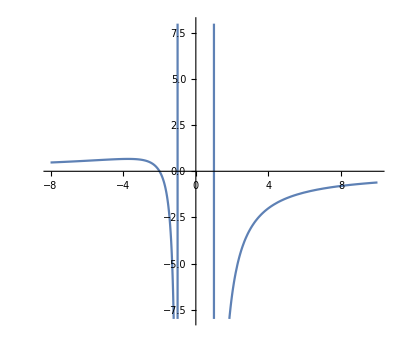

```mathematica
Plot[{y=(5x+10)/(-x^2+1)},{x,-8,10},AspectRatio->Automatic,PlotRange->{-8,8}]
```

10. ZAPOREDJA
Dokaži, da je zaporedje s splošnim členom a_n(8n-3)/(5n+2) naraščajoče.